```mathematica
(* Jack Farrell, Dept. of Physics, University of Toronto, 2020 *)
(* Investigating the frequency and growth rate of the quasinormal modes of the Dyakonov-Shur Instability of viscous electrons in an annular geometry *)

ClearAll[v0,η,γ,ratio,R1,R2,eq1,eq2,u,n,rawVals];
SetDirectory[NotebookDirectory[]];
ratios = Table[i,{i,0.0001,4,0.1}];
freqs=Table[0,{i,1,Length[ratios]}];
rates=Table[0,{i,1,Length[ratios]}];
For[i=1,i<Length[ratios]+1,i++,
v0=0.14;
η=0.1;
γ=0.1;

ratio = ratios[[i]];
R1 = 1/ratio;
R2 = R1+1;

eq1 = D[u[t,r],t]+2*v0*R2*D[u[t,r]/r,r]+r*D[n[t,r],r] - r*η*(D[u[t,r]/r,{r,2}]+1/r*D[u[t,r]/r, r])==-γ*u[t,r]+NeumannValue[0,r==R1];
eq2 = D[n[t,r],t]+1/r*D[u[t,r],r]==0;

rawVals=NDEigenvalues[{eq1,eq2,DirichletCondition[u[t,r]==0,r==R2],DirichletCondition[n[t,r]==0,r==R1]},{u[t,r],n[t,r]},t,{r,R1,R2},10];
vals=Sort[I*rawVals,Abs[Re[#1]-Pi/2]<Abs[Re[#2]-Pi/2]&];
val=vals[[1]];
freqs[[i]]=Re[val];
rates[[i]]=Im[val];
]
```

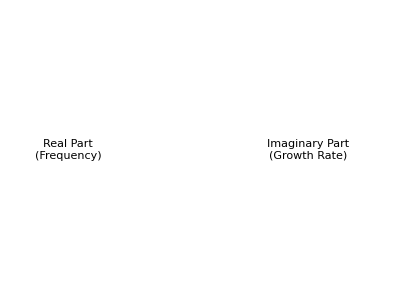

```mathematica
p1=Labeled[Show[ListPlot[Thread[{ratios,freqs}], GridLines->Automatic,PlotStyle->Black], Plot[Pi/2,{x, 0.001, ratios[[Length[ratios]]]}, PlotStyle->Black], PlotRange->All, AxesLabel->{Style[L/Subscript[R, 1], FontWeight->Bold], Style[ω, Bold]}], Style["Real Part
(Frequency)", FontFamily->"Times New Roman"]];
p2=Labeled[Show[ListPlot[Thread[{ratios,rates}],GridLines->Automatic, PlotStyle->Black],Plot[0.106, {x,0,ratios[[Length[ratios]]]}, PlotStyle->Black],AxesLabel->{Style[L/Subscript[R, 1], FontWeight->Bold], Style[ω, Bold]}], Style["Imaginary Part
(Growth Rate)", FontFamily->"Times New Roman"]];
plot1 =GraphicsRow[{p1,p2}]
(*Export["Figures/annular-frequency-growthrate.pdf",plot1]*)
```